# 2D First-Passage time

## Drift towards the equilibrium at (x, y) = (0, 0) with an absorbing boundary at xh=1.

```mathematica
{{1/2,(√(σ/λ))/(2 (1+λ))},{(√(σ/λ))/(2 (1+λ)),(λ+λ^2+σ)/(2 λ+2 λ^2)}}/.params[[3]]
```

{{1/2,0.666667},{0.666667,1.83333}}

```mathematica
xf=10;
tf=12;
```

## Write down the Fokker-Planck equation

```mathematica
FP= D[p[t, x, xh], t]==λ*D[x*p[t, x, xh], x]+D[xh*p[t, x, xh], xh]-Sqrt[σ/λ]*D[x*p[t, x, xh],xh]+λ*D[p[t, x, xh],{x,2}]+D[p[t, x, xh],{xh,2}]
```

p^(1,0,0)[t,x,xh]==p[t,x,xh]+xh p^(0,0,1)[t,x,xh]-x √(σ/λ) p^(0,0,1)[t,x,xh]+p^(0,0,2)[t,x,xh]+λ (p[t,x,xh]+x p^(0,1,0)[t,x,xh])+λ p^(0,2,0)[t,x,xh]

## Choose the parameter values

```mathematica
λs = {0.5, 1, 2};
σs = {0.5, 1, 2};
params = Flatten[Table[{λ->l, σ->s}, {l, λs}, {s, σs}], 1]
legend =  Flatten[Table["λ="<>ToString[l]<>"; "<> "σ="<>ToString[s], {l, λs}, {s, σs}], 1]
```

{{λ→0.5,σ→0.5},{λ→0.5,σ→1},{λ→0.5,σ→2},{λ→1,σ→0.5},{λ→1,σ→1},{λ→1,σ→2},{λ→2,σ→0.5},{λ→2,σ→1},{λ→2,σ→2}}

{λ=0.5; σ=0.5,λ=0.5; σ=1,λ=0.5; σ=2,λ=1; σ=0.5,λ=1; σ=1,λ=1; σ=2,λ=2; σ=0.5,λ=2; σ=1,λ=2; σ=2}

## Write down the boundary conditions

```mathematica
bcs = {p[t,-xf, xh]==0,
           p[t, xf, xh]==0,
           p[t, x, xf]==0,
           p[t, x, 1]==0
}
```

{p[t,-10,xh]==0,p[t,10,xh]==0,p[t,x,10]==0,p[t,x,1]==0}

## And initial condition (distribution with the s.s. covariance, depends on parameters)

```mathematica
icSS = Table[PDF[MultinormalDistribution[{5, 5},({{1/2,σ/(√λ (2+2 λ))},{σ/(√λ (2+2 λ)),(λ+λ^2+σ^2)/(2 λ+2 λ^2)}}/.pa)], {x, xh}],{pa, params}]
```

{0.301975 ⅇ^(1/2 (-(-5+x) (2.4 (-5+x)-0.848528 (-5+xh))-(-0.848528 (-5+x)+1.8 (-5+xh)) (-5+xh))),0.26485 ⅇ^(1/2 (-(-5+x) (3.23077 (-5+x)-1.30543 (-5+xh))-(-1.30543 (-5+x)+1.38462 (-5+xh)) (-5+xh))),0.190986 ⅇ^(1/2 (-(-5+x) (4.56 (-5+x)-1.35765 (-5+xh))-(-1.35765 (-5+x)+0.72 (-5+xh)) (-5+xh))),0.308806 ⅇ^(1/2 (-(-5+x) (2.11765 (-5+x)-0.470588 (-5+xh))-(-0.470588 (-5+x)+1.88235 (-5+xh)) (-5+xh))),(2 ⅇ^(1/2 (-(-5+x) (12/5 (-5+x)-4/5 (-5+xh))-(-4/5 (-5+x)+8/5 (-5+xh)) (-5+xh))))/(√5 π),ⅇ^(1/2 (-(-5+x) (5+3 (-5+x)-xh)-(-5+xh) (-x+xh)))/(√2 π),0.313979 ⅇ^(1/2 (-(-5+x) (2.02703 (-5+x)-0.229332 (-5+xh))-(-0.229332 (-5+x)+1.94595 (-5+xh)) (-5+xh))),(3 ⅇ^(1/2 (3/10 (30-5 √2+√2 x-6 xh) (-5+xh)+3/10 (-5+x) (35-5 √2-7 x+√2 xh))))/(√10 π),(3 ⅇ^(1/2 (6/13 (15-5 √2+√2 x-3 xh) (-5+xh)+6/13 (-5+x) (25-5 √2-5 x+√2 xh))))/(√13 π)}

```mathematica
ic0 = Table[PDF[MultinormalDistribution[{5, 5},({{1/2,(√(σ/λ))/(2 (1+λ))},{(√(σ/λ))/(2 (1+λ)),(λ+λ^2+σ)/(2 λ+2 λ^2)}}/.params[[3]])], {x, xh}], {i, params}]
```

{0.231604 ⅇ^(1/2 (-(-5+x) (3.88235 (-5+x)-1.41176 (-5+xh))-(-1.41176 (-5+x)+1.05882 (-5+xh)) (-5+xh))),0.231604 ⅇ^(1/2 (-(-5+x) (3.88235 (-5+x)-1.41176 (-5+xh))-(-1.41176 (-5+x)+1.05882 (-5+xh)) (-5+xh))),0.231604 ⅇ^(1/2 (-(-5+x) (3.88235 (-5+x)-1.41176 (-5+xh))-(-1.41176 (-5+x)+1.05882 (-5+xh)) (-5+xh))),0.231604 ⅇ^(1/2 (-(-5+x) (3.88235 (-5+x)-1.41176 (-5+xh))-(-1.41176 (-5+x)+1.05882 (-5+xh)) (-5+xh))),0.231604 ⅇ^(1/2 (-(-5+x) (3.88235 (-5+x)-1.41176 (-5+xh))-(-1.41176 (-5+x)+1.05882 (-5+xh)) (-5+xh))),0.231604 ⅇ^(1/2 (-(-5+x) (3.88235 (-5+x)-1.41176 (-5+xh))-(-1.41176 (-5+x)+1.05882 (-5+xh)) (-5+xh))),0.231604 ⅇ^(1/2 (-(-5+x) (3.88235 (-5+x)-1.41176 (-5+xh))-(-1.41176 (-5+x)+1.05882 (-5+xh)) (-5+xh))),0.231604 ⅇ^(1/2 (-(-5+x) (3.88235 (-5+x)-1.41176 (-5+xh))-(-1.41176 (-5+x)+1.05882 (-5+xh)) (-5+xh))),0.231604 ⅇ^(1/2 (-(-5+x) (3.88235 (-5+x)-1.41176 (-5+xh))-(-1.41176 (-5+x)+1.05882 (-5+xh)) (-5+xh)))}

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
mesh=ToElementMesh[Rectangle[{-xf, 1}, {xf, xf}],MaxCellMeasure->0.025 ]
```

ElementMesh[{{-10.,10.},{1.,10.}},{QuadElement[<7239>]}]

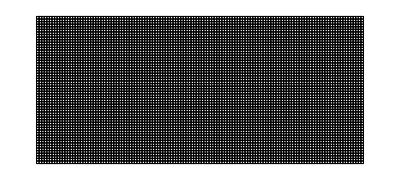

```mathematica
mesh["Wireframe"]
```

```mathematica
NDSolverParams[param_, ic_] :=Module[{N},
N = NDSolve[Join[{(FP/. param),p[0, x,xh]== ic}, bcs],
                                   p,{t,0,tf},Element[{x, xh}, mesh], 
Method->{"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}}];
Return[p/.N[[1]]];
]
```

## Calculate the probability distribution and the flux through the boundary

```mathematica
sols=MapThread[NDSolverParams, {params, ic0}];
flux = Table[Derivative[0,0,1][sol], {sol, sols}];
```

```mathematica
Manipulate[Plot3D[sols[[3]][t, x, xh], {x, -1,xf}, {xh, 1, xf}, AxesLabel->{x, xh}, PlotRange->{-0.01, 0.3}, PlotLegends->Automatic, ColorFunction->ColorData[{"CherryTones",{-0.01,0.2}}],ColorFunctionScaling->False], {t, 0, tf}]
Manipulate[ContourPlot[sols[[4]][t, x, xh], {x, -1,xf}, {xh, 1, xf}, AxesLabel->{x, xh},PlotRange->{-0.01, 0.3}, ColorFunction->ColorData[{"CherryTones",{-0.01,0.2}}],ColorFunctionScaling->False, PlotLegends->Automatic], {t, 0, tf}]
```

## Integrate the flux in t to get q(x)

At a given value of x, integrate in time

```mathematica
xrange = N[Range[-xf/2, xf/2, xf/50]]
```

```mathematica
nintxsolve[xr_, s_]:=Module[{t, x},
n =Table[NDSolveValue[{g'[t]==s[t, x, 1],g[0]==0},g,{t,0,tf}][tf], {x, xr}];
Return[n];
];
```

{-5.,-4.8,-4.6,-4.4,-4.2,-4.,-3.8,-3.6,-3.4,-3.2,-3.,-2.8,-2.6,-2.4,-2.2,-2.,-1.8,-1.6,-1.4,-1.2,-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.}

```mathematica
nintx[xr_, s_]:=Module[{t, eval},
n = Table[NIntegrate[s[t, x,1],{t,0,tf}, Method->{"InterpolationPointsSubdivision","SymbolicProcessing"->0}],{x, xr}];
Return[n];
];
```

{-5.,-4.9,-4.8,-4.7,-4.6,-4.5,-4.4,-4.3,-4.2,-4.1,-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.}

```mathematica
xvals = Table[nintxsolve[xrange,flu], {flu, flux}];
```

Interpolate to get the distribution in x

```mathematica
X=Table[Interpolation[Transpose@{xrange, xval}][x], {xval, xvals}];
```

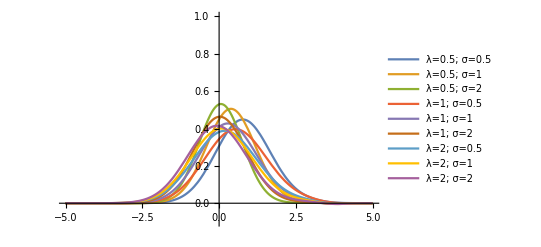

```mathematica
Plot[X, {x, -xf/2, xf/2}, PlotLegends->legend, PlotRange->{-0.1, 1}]
```

```mathematica
norms = Table[NIntegrate[xp, {x, -xf/2, xf/2}, WorkingPrecision->16], {xp, X}]
means = Table[NIntegrate[xp*x, {x, -xf/2, xf/2}, WorkingPrecision->16], {xp, X}];
second = Table[NIntegrate[xp*x*x, {x, -xf/2, xf/2}, WorkingPrecision->16], {xp, X}];
vars = second-means^2
diff = vars/means;
```

{1.01338,1.01135,0.949831,1.00987,1.01031,1.01133,1.00524,1.00868,1.00998}

{0.840538628161589,0.662510005928391,0.496690617803751,1.05481713321755,0.91713185095774,0.782099718552228,1.06337801520534,1.01008838112337,0.943997556776064}

```mathematica
λs = { 0.5, 1, 2};
σs = {0.5, 1, 2};
grid = Flatten[Table[{l, s}, {l, λs}, {s, σs}], 1];
v = Table[{va}, {va, vars}];
```

```mathematica
varArray = ArrayReshape[vars, {3, 3}];
meanArray = ArrayReshape[means, {3, 3}];
diffArray = ArrayReshape[diff, {3, 3}];
```

```mathematica
xticks = Transpose[{{1, 2, 3}, λs}];
yticks = Transpose[{{1, 2, 3}, σs}];
```

```mathematica
ArrayPlot[varArray, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"var(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, σ}]

ArrayPlot[meanArray, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, σ}]

ArrayPlot[diffArray, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"var(x)/mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, σ}]
```

-Graphics-

-Graphics-

-Graphics-

## Integrate to get the survival probability and first-passage times

```mathematica
nintrange[tr_, s_]:=Module[{x, xh},
n = Table[NIntegrate[s[x,xh,t], {x,xh}∈s["ElementMesh"],  Method->"InterpolationPointsSubdivision"],{t, tr}];
Return[n];
];trange = N[Range[0, tf, tf/50]];
```

```mathematica
S= Table[nintrange[trange,sol], {sol, sols}];
```

NIntegrate::femonly: Method InterpolationPointsSubdivision is not applicable for this region domain. Continuing with the "FiniteElement" method.

General::stop: Further output of NIntegrate::femonly will be suppressed during this calculation.

```mathematica
s=Table[Interpolation[Transpose@{trange, Sp}][t], {Sp, S}];
f = Table[-D[sp, t], {sp, s}];
```

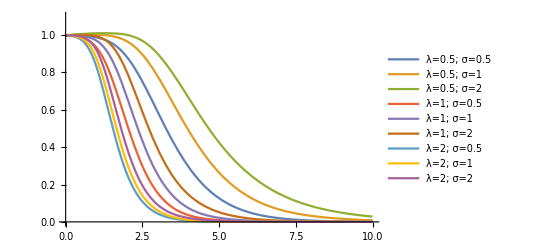

```mathematica
Plot[s,{t, 0, tf}, PlotRange->{0,1.1}, PlotLegends->legend]
```

## Calculate first-passage time probability

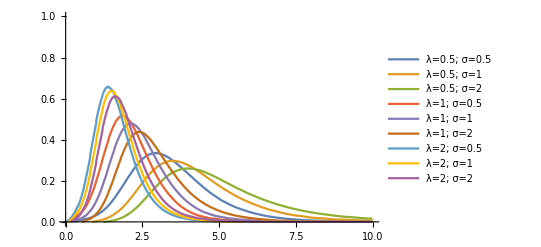

```mathematica
Plot[f,{t, 0, tf}, PlotRange->{0, 1} , PlotLegends->legend]
```

```mathematica
norms = Table[NIntegrate[fp, {t, 0, tf}], {fp, f}]
means = Table[NIntegrate[fp*t, {t, 0, tf}], {fp, f}]
second = Table[NIntegrate[fp*t*t, {t, 0, tf}], {fp, f}]
vars = second-means^2
```

{0.996601,0.988501,0.968595,0.997091,0.997098,0.996506,0.99702,0.997011,0.997015}

{3.45462,4.16734,4.76701,2.15921,2.49471,2.90643,1.63569,1.75965,1.93072}

{13.817,19.8175,25.9578,5.47297,7.21248,9.71744,3.18336,3.64939,4.37198}

{1.88255,2.45074,3.23341,0.810779,0.988891,1.27009,0.507871,0.553031,0.644305}